# Neural Logic Networks

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## A regression problem

```mathematica
data=ResourceData["7307b047-05ec-4d46-b3c9-9995faf75130"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

## Utilities

### Feature encoders

```mathematica
FeatureValues[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->Last[#]&/@featureValues]
]
featureValues=FeatureValues[trainData];
```

```mathematica
encoders=Map[RealEncoderDecoder[#, 32]&,featureValues];
```

```mathematica
standardNetInputSize=Length[encoders]-1
```

11

```mathematica
standardFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],1]},NetGraph[
<|
Splice[Map[#->ReshapeLayer[{1},"Input"->{}]&,Keys[inputEncoders]]],
"Catenate"->CatenateLayer["Output"->standardNetInputSize]
|>,
Join[
Map[#->"Catenate"&,Keys[inputEncoders]],
Map[NetPort[#]->#&,Keys[inputEncoders]]
]
]]
```

NetGraph[<>]

```mathematica
neuralLogicFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],1]},NetGraph[
<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[#]->"Catenate"&,Keys[inputEncoders]],
Sequence@@Normal[Drop[Normal[#["NetEncoder"]&/@encoders],1]]
]]
```

NetGraph[<>]

```mathematica
exampleInputFeature=neuralLogicFeatureLayer[Normal[Drop[trainData[[1]],1]]]
```

{0.,0.,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,1.,1.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,0.,1.,1.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,1.,1.,0.,0.,0.,1.,0.,1.,0.,0.,1.,0.,0.,0.,1.,0.,0.,1.,1.,0.,0.,0.,1.,0.,1.,0.,0.,1.,0.,0.,1.,0.,1.,1.,0.,0.,0.,0.,1.,1.,0.,0.}

```mathematica
neuralLogicInputSize=Length[exampleInputFeature]
```

84

### Define standard net

```mathematica
StandardNet[]:=Module[{standardNet},
standardNet=NetChain[{
LinearLayer[256,"Input"->standardNetInputSize],
ElementwiseLayer["ScaledExponentialLinearUnit"],
LinearLayer[256],
ElementwiseLayer["ScaledExponentialLinearUnit"],
LinearLayer[1]
}];
NetGraph[
<|
"Features"->standardFeatureLayer,
"Net"->standardNet,
"Reshape"->ReshapeLayer[{}]
|>,
{"Features"->"Net","Net"->"Reshape",NetPort["Reshape","Output"]->NetPort["WineQuality"]}
]
]
```

### Train standard net

```mathematica
TrainStandardNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
MaxTrainingRounds->Infinity,
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real32"]
```

### Evaluate standard net

```mathematica
StandardNetPredict[trainedNet_,data_,targetName_]:=Module[{prediction},
prediction=ResourceFunction["DynamicMap"][<|
"Prediction"->trainedNet[#],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

```mathematica
GetStandardWeights[trainedStandardNet_]:=Module[{},
Flatten[Normal/@DeleteMissing[Values[Quiet[NetExtract[NetFlatten[trainedStandardNet],{All,"Weights"}]]]]]
]
```

### Define neural logic net

```mathematica
NeuralLogicNet[]:=Module[{size=3*128,softNet,hardNet,net,trainableNet},
{softNet,hardNet}=HardNeuralChain[{
HardNeuralNOT[neuralLogicInputSize,size],
HardNeuralOR[neuralLogicInputSize,size],
HardNeuralReshapeLayer[size,encoders["WineQuality"]["NumBits"]],
NeuralHardeningLayer[],
{AggregationLayer[Mean],#&}
}];
trainableNet=NetGraph[
<|
"FeatureLayer"->neuralLogicFeatureLayer,
"SoftNet"->softNet,
"Hardening"->HardeningLayer[]
|>,
{
"FeatureLayer"->"SoftNet",
"SoftNet"->"Hardening",
NetPort["Hardening","Output"]->NetPort["WineQuality"]
(*NetPort["SoftNet","Output"]->NetPort["WineQuality"]*)
}
];
{trainableNet,hardNet}
]
```

```mathematica
NeuralLogicNet[][[1]]
```

NetGraph[<>]

```mathematica
With[{size=192},HardNeuralChain[{
HardNeuralNOT[neuralLogicInputSize,size],
HardNeuralOR[neuralLogicInputSize,size],
HardNeuralNOT[size,size],
HardNeuralOR[size,size],
HardNeuralReshapeLayer[size,encoders["WineQuality"]["NumBits"]],
NeuralHardeningLayer[],
{AggregationLayer[Mean],#&}
}]][[1]]
```

NetChain[<>]

### Train neural logic net

```mathematica
TrainNeuralLogicNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
LossFunction->MeanSquaredLossLayer["Target"->encoders["WineQuality"]["NetEncoder"]],
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real64",
MaxTrainingRounds->Infinity]
```

### Evaluate neural logic net

```mathematica
GetNeuralLogicWeights[trainedNeuralLogicNet_]:=Harden[Flatten[ExtractWeights[trainedNeuralLogicNet]]]
```

## A standard neural network

```mathematica
(*
p=Predict[trainData->"WineQuality",PerformanceGoal->"Quality",Method->"NeuralNetwork"];
pm=PredictorMeasurements[p,testData]
*)
```

```mathematica
standardNet=StandardNet[]
```

NetGraph[<>]

```mathematica
result=TrainStandardNet[standardNet,trainData,testData];
```

```mathematica
trainedStandardNet=result["TrainedNet"];
```

```mathematica
NetMeasurements[trainedStandardNet,testData,{"RSquared","FractionVarianceUnexplained" ,"MeanDeviation","MeanSquare","StandardDeviation"}]
```

{0.283855,0.716145,0.569921,0.52907,0.727372}

```mathematica
standardPredictions=StandardNetPredict[trainedStandardNet,testData,"WineQuality"];
```

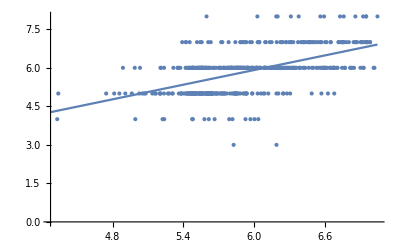

```mathematica
ResourceFunction["RegressionListPlot"][Values/@standardPredictions]
```

```mathematica
standardWeights=GetStandardWeights[trainedStandardNet];
```

```mathematica
standardNetSize=Quantity[Length[standardWeights]*32/1024.0,"Kilobytes"]
```

2144. kB

## A neural logic network

```mathematica
{softNet,hardNet}=NeuralLogicNet[];
```

```mathematica
NetFlatten[softNet]
```

NetGraph[<>]

```mathematica
result=TrainNeuralLogicNet[softNet,trainData,testData];
```

```mathematica
trainedNeuralLogicNet=NetGraph[{1->result["TrainedNet"],2->SoftBitVectorToRealLayer[encoders["WineQuality"]["NumBits"],encoders["WineQuality"]["MinMax"]]},{1->2,NetPort[2,"Output"]->NetPort["WineQuality"]}]
```

$Failed

```mathematica
NetMeasurements[trainedNeuralLogicNet,testData,{"RSquared","FractionVarianceUnexplained" ,"MeanDeviation","MeanSquare","StandardDeviation"}]
```

{-3.37985,4.37985,1.75306,3.81735,1.9538}

```mathematica
neuralLogicPredictions=StandardNetPredict[trainedNeuralLogicNet,testData,"WineQuality"];
```

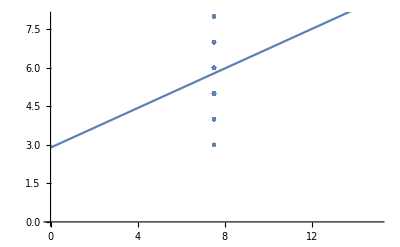

```mathematica
ResourceFunction["RegressionListPlot"][Values/@neuralLogicPredictions]
```

```mathematica
hnf=HardNetFunction[hardNet,trainedNeuralLogicNet];
hnbe=HardNetBooleanExpression[hnf,neuralLogicInputSize]
```

```mathematica
encoders["WineQuality"]["DecoderFunction"]
```

SoftBitVectorToReal[Normal[#1],{3,9}]&

```mathematica
NeuralLogicPredict[data_,encoders_,targetName_,hardNetFunction_,featureLayer_]:=Module[{booleanPrediction},
booleanPrediction=ResourceFunction["DynamicMap"][<|
"Prediction"->N[encoders["WineQuality"]["DecoderFunction"][Boole[hardNetFunction[Harden[Normal[featureLayer[#]]]]]]],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

```mathematica
predictions=NeuralLogicPredict[testData,encoders,"WineQuality",hnf,neuralLogicFeatureLayer]
```

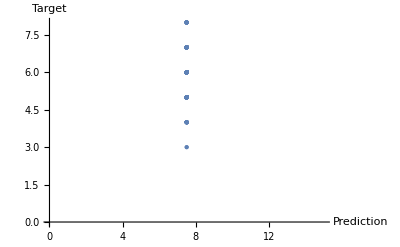

```mathematica
ListPlot[predictions,AxesLabel->Automatic]
```

```mathematica
neuralLogicWeights=GetNeuralLogicWeights[result["TrainedNet"]];
```

```mathematica
neuralLogicNetSize=Quantity[Length[neuralLogicWeights]/8/1024//N,"Kilobytes"]
```

29.3438 kB

```mathematica
standardNetSize/neuralLogicNetSize
```

80.

## Notes

```mathematica
Table[2^i,{i,8-1,0,-1}]
```

```mathematica
{1,0,0,1,0,0,1,1}{128,64,32,16,8,4,2,1}
```

{128,0,0,16,0,0,2,1}

```mathematica
btr=BinaryToReal[8,{0.0,255.0}];
```

```mathematica
btr[{1,0,0,0,0,0,0,0}]
```

255.

```mathematica
btr[{1,0,0,0,0,1,1,0}]
```

255.

```mathematica
btr[{0,1,1,1,1,0,0,0}]
```

239.063

```mathematica
FunctionLayer[btr]
```

$Failed

```mathematica
btr=BinaryToReal[8,{0.0,255.0}]
```

Function[{Typed[neurallogic`Private`input,TypeSpecifier[PackedArray][MachineReal,1]]},Module[{neurallogic`Private`y$},neurallogic`Private`y$=Total[neurallogic`Private`input Table[2^(neurallogic`Private`i),{neurallogic`Private`i,8-1,0,-1}]];neurallogic`Private`y$=1. neurallogic`Private`y$;neurallogic`Private`y$=(neurallogic`Private`y$)/2^(8-1);neurallogic`Private`y$=(255.-0.) neurallogic`Private`y$+0.;Clip[neurallogic`Private`y$,{0.,255.}]]]

```mathematica
sbvtrl=SoftBitVectorToRealLayer[8,{0,255}]
```

NetGraph[<>]

```mathematica
sbvtrl[{0,1,1,1,1,0,0,0}]
```

239.063

```mathematica
sbvtrl[{0.1,0.6,0.6,0.6,0.6,0,0,0}]
```

239.063